```mathematica
data=Transpose[Import["C:\\Users\\Abigail\\Desktop\\Wolfram data\\Cestode\\Data_cestode.csv"]];
```

```mathematica
hdr=data//First
```

{Classification,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Species,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family}

```mathematica
Dimensions[data]
```

{7,149}

```mathematica
cestode12S=data[[2,2;;149]]
cestode16S=data[[3,2;;149]]
cestodeCOI=data[[4,2;;149]]
cestodeCOII=data[[5,2;;149]]
cestodecytb=data[[6,2;;149]]
cestodeND=data[[7,2;;149]]
```

{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107,0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175,0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}

{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112,0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.21,0.193,0.212}

{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105,0.194,0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.206,0.216,0.178,0.215,0.204,0.19,0.214,0.206,0.189,0.205,0.202,0.174,0.212,0.214,0.18,0.212,0.214,0.18,0.21,0.21,0.183,0.212,0.214,0.179,0.206,0.211,0.178,0.207,0.21,0.176,0.212,0.21,0.183,0.211,0.21,0.182,0.211,0.205,0.18,0.207,0.208,0.175,0.21,0.202,0.171,0.202,0.202,0.17,0.206,0.208}

{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134,0.258,0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.266,0.273,0.225,0.267,0.267,0.21,0.262,0.266,0.2,0.283,0.299,0.241,0.283,0.303,0.23,0.282,0.303,0.228,0.271,0.312,0.219,0.285,0.301,0.228,0.28,0.296,0.232,0.28,0.296,0.232,0.269,0.308,0.217,0.271,0.31,0.219,0.283,0.305,0.216,0.287,0.298,0.228,0.287,0.305,0.228,0.275,0.294,0.235,0.266,0.285}

{0.148,0.144,0.041,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.003,0.002,0.068,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.069,0.12,0.106,0.12,0.068,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13,0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}

{0.132,0.13,0.048,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.006,0.006,0.07,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.064,0.135,0.148,0.153,0.064,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159,0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}

```mathematica
Stat[clusterdata_]:={Mean[#],StandardDeviation[#],MinMax[#]}&/@clusterdata
```

```mathematica
PlotCluster[clusterdata_,plotlabel_]:=ListPlot[clusterdata,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Frame->True,FrameLabel->{"Samples","Genetic Distance"},GridLines->Automatic,ImageSize->Medium,PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green},{PointSize[Medium],Blue}},PlotLabel->plotlabel]
```

```mathematica
{clstrcestode12S,clstrcestode16S,clstrcestodeCOI,clstrcestodeCOII,clstrcestodecytb,clstrcestodeND}=FindClusters[#,3,Method->"KMeans"]&/@{cestode12S,cestode16S,cestodeCOI,cestodeCOII,cestodecytb,cestodeND};
```

```mathematica
Stat[clstrcestode12S]
```

{{0.0811507,0.0222072,{0,0.116}},{0.15932,0.00859612,{0.139,0.175}},{0.21668,0.012313,{0.194,0.237}}}

```mathematica
statdata=Stat/@{clstrcestode12S,clstrcestode16S,clstrcestodeCOI,clstrcestodeCOII,clstrcestodecytb,clstrcestodeND}
```

{{{0.0811507,0.0222072,{0,0.116}},{0.15932,0.00859612,{0.139,0.175}},{0.21668,0.012313,{0.194,0.237}}},{{0.0796027,0.0231953,{0.001,0.112}},{0.191037,0.00827639,{0.178,0.21}},{0.231042,0.0112457,{0.212,0.253}}},{{0.0835068,0.0196371,{0.003,0.116}},{0.208,0.00557546,{0.19,0.216}},{0.171154,0.00838086,{0.149,0.189}}},{{0.11089,0.0252359,{0.004,0.148}},{0.285029,0.0155629,{0.258,0.312}},{0.212325,0.0136821,{0.191,0.241}}},{{0.114328,0.0138174,{0.09,0.148}},{0.0418333,0.0322578,{0.002,0.069}},{0.257507,0.0324122,{0.197,0.299}}},{{0.139478,0.0127343,{0.103,0.168}},{0.043,0.029577,{0.006,0.07}},{0.25304,0.0213646,{0.214,0.287}}}}

```mathematica
MySort[clusterdata_]:=Module[{len,max,or},
len=Length@clusterdata;
max=Max/@clusterdata;
or=Ordering[max];
clusterdata[[or]]
];
```

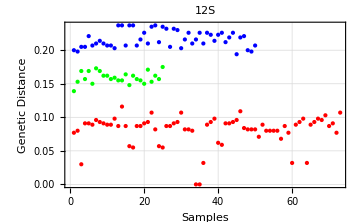

```mathematica
PlotCluster[MySort[clstrcestode12S],"12S"]
```

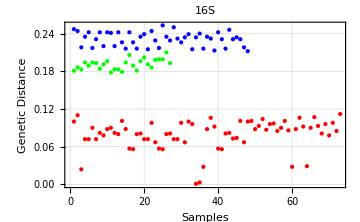

```mathematica
PlotCluster[MySort[clstrcestode16S],"16S"]
```

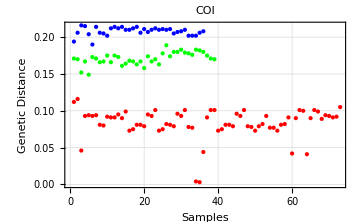

```mathematica
PlotCluster[MySort[clstrcestodeCOI],"COI"]
```

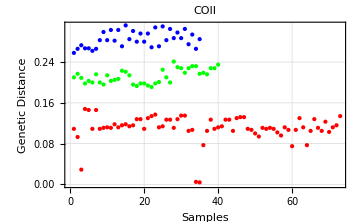

```mathematica
PlotCluster[MySort[clstrcestodeCOII],"COII"]
```

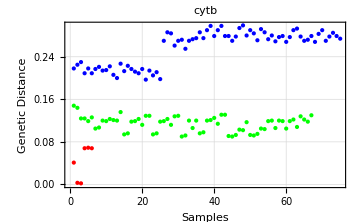

```mathematica
PlotCluster[MySort[clstrcestodecytb],"cytb"]
```

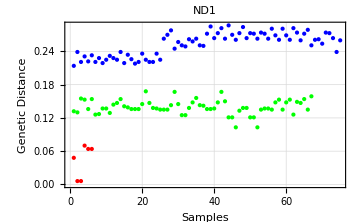

```mathematica
PlotCluster[MySort[clstrcestodeND],"ND1"]
```

```mathematica
Grid[Partition[PlotCluster/@MySort/@{clstrcestode12S,clstrcestode16S,clstrcestodeCOI,clstrcestodeCOII,clstrcestodecytb,clstrcestodeND},3]]
```

PlotCluster[{{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107},{0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175},{0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}}] | PlotCluster[{{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112},{0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.21,0.193},{0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.212}}] | PlotCluster[{{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105},{0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.178,0.189,0.174,0.18,0.18,0.183,0.179,0.178,0.176,0.183,0.182,0.18,0.175,0.171,0.17},{0.194,0.206,0.216,0.215,0.204,0.19,0.214,0.206,0.205,0.202,0.212,0.214,0.212,0.214,0.21,0.21,0.212,0.214,0.206,0.211,0.207,0.21,0.212,0.21,0.211,0.21,0.211,0.205,0.207,0.208,0.21,0.202,0.202,0.202,0.206,0.208}}]
PlotCluster[{{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134},{0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.225,0.21,0.2,0.241,0.23,0.228,0.219,0.228,0.232,0.232,0.217,0.219,0.216,0.228,0.228,0.235},{0.258,0.266,0.273,0.267,0.267,0.262,0.266,0.283,0.299,0.283,0.303,0.282,0.303,0.271,0.312,0.285,0.301,0.28,0.296,0.28,0.296,0.269,0.308,0.271,0.31,0.283,0.305,0.287,0.298,0.287,0.305,0.275,0.294,0.266,0.285}}] | PlotCluster[{{0.041,0.003,0.002,0.068,0.069,0.068},{0.148,0.144,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.12,0.106,0.12,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13},{0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}}] | PlotCluster[{{0.048,0.006,0.006,0.07,0.064,0.064},{0.132,0.13,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.135,0.148,0.153,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159},{0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}}]

```mathematica
FindClusters[cestode12S,3,Method->"KMeans"]
```

{{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107},{0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175},{0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}}

```mathematica
Mean[{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107}]
```

0.0811507

```mathematica
StandardDeviation[{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107}]
```

0.0222072

```mathematica
MinMax[{0.077,0.08,0.03,0.091,0.091,0.089,0.096,0.093,0.091,0.089,0.089,0.098,0.087,0.116,0.087,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.057,0.055,0.087,0.087,0.091,0.093,0.107,0.082,0.082,0.08,0,0,0.032,0.089,0.093,0.098,0.062,0.059,0.091,0.091,0.093,0.096,0.109,0.084,0.082,0.082,0.082,0.071,0.089,0.08,0.08,0.08,0.08,0.068,0.087,0.077,0.032,0.089,0.093,0.098,0.032,0.089,0.093,0.098,0.096,0.103,0.087,0.091,0.077,0.107}]
```

{0,0.116}

```mathematica
Mean[{0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175}]
```

0.15932

```mathematica
NumberForm[0.08440983606557376,16]
```

0.0844098360655737

```mathematica
StandardDeviation[{0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175}]
```

0.00859612

```mathematica
MinMax[{0.139,0.153,0.169,0.157,0.169,0.15,0.173,0.169,0.162,0.162,0.157,0.159,0.155,0.155,0.164,0.148,0.162,0.157,0.155,0.15,0.171,0.153,0.162,0.157,0.175}]
```

{0.139,0.175}

```mathematica
Mean[{0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}]
```

0.21668

```mathematica
StandardDeviation[{0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}]
```

0.012313

```mathematica
MinMax[{0.2,0.198,0.205,0.205,0.221,0.207,0.21,0.214,0.21,0.207,0.207,0.203,0.237,0.237,0.207,0.237,0.237,0.207,0.216,0.226,0.21,0.235,0.237,0.212,0.235,0.232,0.205,0.232,0.23,0.203,0.216,0.226,0.21,0.216,0.226,0.21,0.226,0.223,0.214,0.223,0.226,0.212,0.219,0.226,0.194,0.219,0.221,0.2,0.198,0.207}]
```

{0.194,0.237}

```mathematica
ListPlot[FindClusters[cestode12S,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

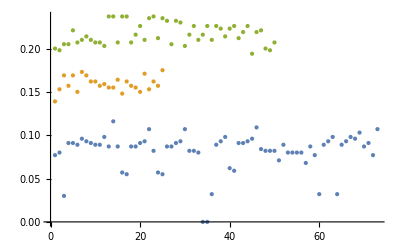

```mathematica
FindClusters[cestode16S,3,Method->"KMeans"]
```

{{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112},{0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.21,0.193},{0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.212}}

```mathematica
Mean[{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112}]
```

0.0796027

```mathematica
StandardDeviation[{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112}]
```

0.0231953

```mathematica
MinMax[{0.1,0.11,0.024,0.072,0.072,0.09,0.072,0.082,0.078,0.088,0.09,0.082,0.08,0.101,0.088,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.057,0.056,0.08,0.081,0.072,0.072,0.098,0.067,0.1,0.096,0.001,0.003,0.028,0.088,0.106,0.092,0.057,0.056,0.081,0.082,0.073,0.074,0.101,0.067,0.1,0.101,0.088,0.093,0.104,0.087,0.096,0.097,0.085,0.09,0.101,0.086,0.028,0.088,0.106,0.092,0.029,0.09,0.107,0.093,0.081,0.096,0.078,0.098,0.085,0.112}]
```

{0.001,0.112}

```mathematica
Mean[{0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.21,0.193}]
```

0.191037

```mathematica
StandardDeviation[{0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.21,0.193}]
```

0.00827639

```mathematica
MinMax[{0.181,0.186,0.183,0.194,0.189,0.194,0.193,0.184,0.191,0.196,0.178,0.183,0.183,0.179,0.194,0.206,0.189,0.181,0.196,0.202,0.191,0.186,0.198,0.199,0.199,0.21,0.193}]
```

{0.178,0.21}

```mathematica
Mean[{0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.212}]
```

0.231042

```mathematica
StandardDeviation[{0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.212}]
```

0.0112457

```mathematica
MinMax[{0.247,0.244,0.218,0.235,0.242,0.217,0.231,0.242,0.22,0.242,0.241,0.22,0.242,0.226,0.216,0.242,0.226,0.216,0.235,0.239,0.215,0.244,0.229,0.217,0.253,0.235,0.229,0.25,0.232,0.226,0.234,0.239,0.215,0.234,0.24,0.216,0.235,0.232,0.213,0.242,0.231,0.216,0.246,0.231,0.234,0.231,0.218,0.212}]
```

{0.212,0.253}

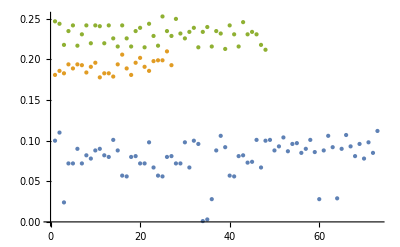

```mathematica
ListPlot[FindClusters[cestode16S,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
FindClusters[cestodeCOI,3,Method->"KMeans"]
```

{{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105},{0.194,0.206,0.216,0.215,0.204,0.19,0.214,0.206,0.205,0.202,0.212,0.214,0.212,0.214,0.21,0.21,0.212,0.214,0.206,0.211,0.207,0.21,0.212,0.21,0.211,0.21,0.211,0.205,0.207,0.208,0.21,0.202,0.202,0.202,0.206,0.208},{0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.178,0.189,0.174,0.18,0.18,0.183,0.179,0.178,0.176,0.183,0.182,0.18,0.175,0.171,0.17}}

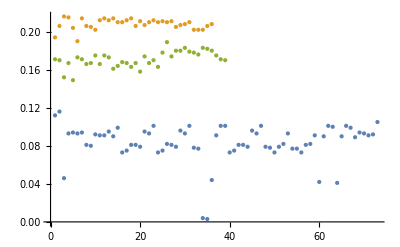

```mathematica
ListPlot[FindClusters[cestodeCOI,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105}]
```

0.0835068

```mathematica
StandardDeviation[{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105}]
```

0.0196371

```mathematica
MinMax[{0.112,0.116,0.046,0.093,0.094,0.093,0.094,0.081,0.08,0.092,0.091,0.091,0.095,0.09,0.099,0.073,0.075,0.081,0.081,0.079,0.095,0.093,0.101,0.073,0.075,0.082,0.081,0.079,0.096,0.093,0.101,0.078,0.077,0.004,0.003,0.044,0.091,0.101,0.101,0.073,0.075,0.081,0.081,0.079,0.096,0.093,0.101,0.079,0.078,0.073,0.079,0.082,0.093,0.077,0.077,0.073,0.081,0.082,0.091,0.042,0.09,0.101,0.1,0.041,0.09,0.101,0.099,0.089,0.094,0.093,0.091,0.092,0.105}]
```

{0.003,0.116}

```mathematica
Mean[{0.194,0.206,0.216,0.215,0.204,0.19,0.214,0.206,0.205,0.202,0.212,0.214,0.212,0.214,0.21,0.21,0.212,0.214,0.206,0.211,0.207,0.21,0.212,0.21,0.211,0.21,0.211,0.205,0.207,0.208,0.21,0.202,0.202,0.202,0.206,0.208}]
```

0.208

```mathematica
StandardDeviation[{0.194,0.206,0.216,0.215,0.204,0.19,0.214,0.206,0.205,0.202,0.212,0.214,0.212,0.214,0.21,0.21,0.212,0.214,0.206,0.211,0.207,0.21,0.212,0.21,0.211,0.21,0.211,0.205,0.207,0.208,0.21,0.202,0.202,0.202,0.206,0.208}]
```

0.00557546

```mathematica
MinMax[{0.194,0.206,0.216,0.215,0.204,0.19,0.214,0.206,0.205,0.202,0.212,0.214,0.212,0.214,0.21,0.21,0.212,0.214,0.206,0.211,0.207,0.21,0.212,0.21,0.211,0.21,0.211,0.205,0.207,0.208,0.21,0.202,0.202,0.202,0.206,0.208}]
```

{0.19,0.216}

```mathematica
Mean[{0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.178,0.189,0.174,0.18,0.18,0.183,0.179,0.178,0.176,0.183,0.182,0.18,0.175,0.171,0.17}]
```

0.171154

```mathematica
StandardDeviation[{0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.178,0.189,0.174,0.18,0.18,0.183,0.179,0.178,0.176,0.183,0.182,0.18,0.175,0.171,0.17}]
```

0.00838086

```mathematica
MinMax[{0.171,0.17,0.152,0.167,0.149,0.173,0.171,0.166,0.167,0.175,0.166,0.175,0.173,0.161,0.164,0.168,0.167,0.163,0.167,0.158,0.174,0.167,0.17,0.163,0.178,0.189,0.174,0.18,0.18,0.183,0.179,0.178,0.176,0.183,0.182,0.18,0.175,0.171,0.17}]
```

{0.149,0.189}

```mathematica
FindClusters[cestodeCOII,3,Method->"KMeans"]
```

{{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134},{0.258,0.266,0.273,0.267,0.267,0.262,0.266,0.283,0.299,0.283,0.303,0.282,0.303,0.271,0.312,0.285,0.301,0.28,0.296,0.28,0.296,0.269,0.308,0.271,0.31,0.283,0.305,0.287,0.298,0.287,0.305,0.275,0.294,0.266,0.285},{0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.225,0.21,0.2,0.241,0.23,0.228,0.219,0.228,0.232,0.232,0.217,0.219,0.216,0.228,0.228,0.235}}

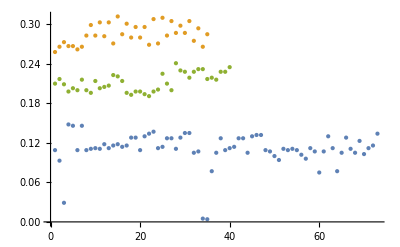

```mathematica
ListPlot[FindClusters[cestodeCOII,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134}]
```

0.11089

```mathematica
StandardDeviation[{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134}]
```

0.0252359

```mathematica
MinMax[{0.109,0.093,0.029,0.148,0.146,0.109,0.146,0.109,0.111,0.112,0.111,0.118,0.112,0.116,0.118,0.114,0.116,0.128,0.128,0.109,0.13,0.134,0.137,0.112,0.114,0.127,0.127,0.111,0.128,0.135,0.135,0.105,0.107,0.005,0.004,0.077,0.105,0.127,0.109,0.112,0.114,0.127,0.127,0.105,0.13,0.132,0.132,0.109,0.107,0.1,0.094,0.111,0.109,0.111,0.109,0.102,0.096,0.112,0.107,0.075,0.107,0.13,0.112,0.077,0.105,0.128,0.111,0.105,0.123,0.103,0.112,0.116,0.134}]
```

{0.004,0.148}

```mathematica
Mean[{0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.225,0.21,0.2,0.241,0.23,0.228,0.219,0.228,0.232,0.232,0.217,0.219,0.216,0.228,0.228,0.235}]
```

0.212325

```mathematica
StandardDeviation[{0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.225,0.21,0.2,0.241,0.23,0.228,0.219,0.228,0.232,0.232,0.217,0.219,0.216,0.228,0.228,0.235}]
```

0.0136821

```mathematica
MinMax[{0.21,0.217,0.209,0.198,0.203,0.2,0.216,0.2,0.196,0.214,0.203,0.205,0.207,0.223,0.221,0.214,0.196,0.193,0.198,0.198,0.194,0.191,0.198,0.201,0.225,0.21,0.2,0.241,0.23,0.228,0.219,0.228,0.232,0.232,0.217,0.219,0.216,0.228,0.228,0.235}]
```

{0.191,0.241}

```mathematica
Mean[{0.258,0.266,0.273,0.267,0.267,0.262,0.266,0.283,0.299,0.283,0.303,0.282,0.303,0.271,0.312,0.285,0.301,0.28,0.296,0.28,0.296,0.269,0.308,0.271,0.31,0.283,0.305,0.287,0.298,0.287,0.305,0.275,0.294,0.266,0.285}]
```

0.285029

```mathematica
StandardDeviation[{0.258,0.266,0.273,0.267,0.267,0.262,0.266,0.283,0.299,0.283,0.303,0.282,0.303,0.271,0.312,0.285,0.301,0.28,0.296,0.28,0.296,0.269,0.308,0.271,0.31,0.283,0.305,0.287,0.298,0.287,0.305,0.275,0.294,0.266,0.285}]
```

0.0155629

```mathematica
MinMax[{0.258,0.266,0.273,0.267,0.267,0.262,0.266,0.283,0.299,0.283,0.303,0.282,0.303,0.271,0.312,0.285,0.301,0.28,0.296,0.28,0.296,0.269,0.308,0.271,0.31,0.283,0.305,0.287,0.298,0.287,0.305,0.275,0.294,0.266,0.285}]
```

{0.258,0.312}

```mathematica
FindClusters[cestodecytb,3,Method->"KMeans"]
```

{{0.148,0.144,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.12,0.106,0.12,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13},{0.041,0.003,0.002,0.068,0.069,0.068},{0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}}

```mathematica
Mean[{0.041,0.003,0.002,0.068,0.069,0.068}]
```

0.0418333

```mathematica
StandardDeviation[{0.041,0.003,0.002,0.068,0.069,0.068}]
```

0.0322578

```mathematica
MinMax[{0.041,0.003,0.002,0.068,0.069,0.068}]
```

{0.002,0.069}

```mathematica
Mean[{0.148,0.144,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.12,0.106,0.12,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13}]
```

0.114328

```mathematica
StandardDeviation[{0.148,0.144,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.12,0.106,0.12,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13}]
```

0.0138174

```mathematica
MinMax[{0.148,0.144,0.124,0.124,0.119,0.126,0.105,0.107,0.12,0.119,0.123,0.121,0.12,0.136,0.094,0.096,0.118,0.119,0.123,0.112,0.129,0.129,0.094,0.096,0.118,0.119,0.123,0.112,0.128,0.129,0.09,0.092,0.12,0.106,0.12,0.096,0.098,0.12,0.121,0.125,0.114,0.131,0.131,0.091,0.09,0.093,0.103,0.102,0.117,0.093,0.092,0.095,0.105,0.104,0.119,0.12,0.106,0.12,0.119,0.105,0.119,0.122,0.108,0.128,0.122,0.118,0.13}]
```

{0.09,0.148}

```mathematica
Mean[{0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}]
```

0.257507

```mathematica
StandardDeviation[{0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}]
```

0.0324122

```mathematica
MinMax[{0.218,0.225,0.23,0.209,0.218,0.209,0.217,0.221,0.214,0.215,0.222,0.206,0.2,0.227,0.213,0.223,0.217,0.212,0.209,0.217,0.197,0.214,0.205,0.211,0.198,0.27,0.286,0.284,0.261,0.27,0.272,0.255,0.27,0.273,0.275,0.286,0.275,0.29,0.298,0.279,0.29,0.298,0.279,0.279,0.27,0.278,0.294,0.299,0.28,0.29,0.284,0.271,0.292,0.286,0.273,0.28,0.269,0.277,0.279,0.268,0.277,0.29,0.293,0.278,0.27,0.272,0.279,0.268,0.283,0.29,0.27,0.278,0.285,0.279,0.274}]
```

{0.197,0.299}

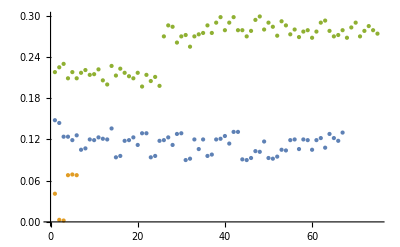

```mathematica
ListPlot[FindClusters[cestodecytb,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
FindClusters[cestodeND,3,Method->"KMeans"]
```

{{0.132,0.13,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.135,0.148,0.153,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159},{0.048,0.006,0.006,0.07,0.064,0.064},{0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}}

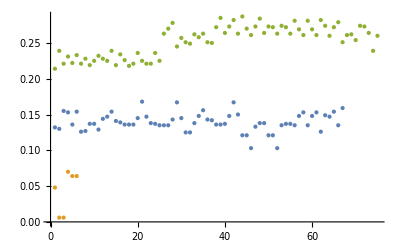

```mathematica
ListPlot[FindClusters[cestodeND,3,Method->"KMeans"],PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.048,0.006,0.006,0.07,0.064,0.064}]
```

0.043

```mathematica
StandardDeviation[{0.048,0.006,0.006,0.07,0.064,0.064}]
```

0.029577

```mathematica
MinMax[{0.048,0.006,0.006,0.07,0.064,0.064}]
```

{0.006,0.07}

```mathematica
Mean[{0.132,0.13,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.135,0.148,0.153,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159}]
```

0.139478

```mathematica
StandardDeviation[{0.132,0.13,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.135,0.148,0.153,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159}]
```

0.0127343

```mathematica
MinMax[{0.132,0.13,0.155,0.153,0.136,0.154,0.126,0.127,0.137,0.137,0.129,0.144,0.147,0.154,0.141,0.139,0.136,0.136,0.136,0.145,0.168,0.147,0.138,0.137,0.135,0.135,0.135,0.143,0.167,0.145,0.125,0.125,0.138,0.148,0.156,0.143,0.142,0.136,0.136,0.137,0.148,0.167,0.15,0.121,0.121,0.103,0.133,0.138,0.138,0.121,0.121,0.103,0.135,0.137,0.137,0.135,0.148,0.153,0.135,0.148,0.153,0.126,0.149,0.147,0.154,0.135,0.159}]
```

{0.103,0.168}

```mathematica
Mean[{0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}]
```

0.25304

```mathematica
StandardDeviation[{0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}]
```

0.0213646

```mathematica
MinMax[{0.214,0.239,0.221,0.231,0.222,0.233,0.221,0.228,0.219,0.225,0.232,0.228,0.225,0.239,0.219,0.234,0.226,0.218,0.221,0.236,0.225,0.221,0.221,0.236,0.225,0.263,0.27,0.278,0.245,0.257,0.251,0.249,0.262,0.258,0.263,0.251,0.25,0.272,0.285,0.264,0.273,0.282,0.263,0.287,0.27,0.261,0.273,0.284,0.264,0.273,0.272,0.263,0.274,0.272,0.263,0.281,0.269,0.261,0.281,0.269,0.261,0.282,0.274,0.26,0.272,0.279,0.251,0.261,0.262,0.254,0.274,0.273,0.264,0.239,0.26}]
```

{0.214,0.287}